# Towards a Minimal Model for Computer Security

## Willem Nielsen

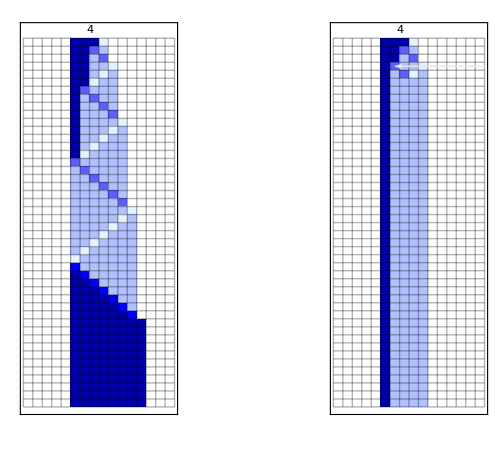

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
{ca, capert} = First[[rule, {Join[Table[1,3],{2}],0},{45,{-5, 10}}, #]]&/@ {<||>, pert};
GraphicsRow[MapThread[Show[{{"[◼]", "PerturbedArrayPlot"}}[#1, #2,ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.3], "ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, "InitialIndex"->0, ImageSize->175,
Frame->False,
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],FrameTicks->{False,  False, False,({{1 + #,"", {-.01, .05}}, {5 + #, "", {-.01, .05}}}&[4.5])}], Graphics[Text["4", {7, Length[ca] + 1}]], Frame->True, PlotRangePadding->{{Automatic, Automatic}, {Automatic, -.75}}] &,{{ca, capert},  {{}, First[Keys[pert]]}}
], Spacings->100]]
```

### Motivation & Goal

I was lucky to work with Stephen Wolfram (creator of Mathematica and Wolfram|Alpha) on his recent research. His work is centered on minimal computational models, in contrast to most theoretical scientists who use mathematical models.

While I was working with him, he suggested to me to use these computational systems to try to model the high-level aspects of computer security. I thought this project would be a good opportunity to do this.

In this article, I will use cellular automata, one of Stephen’s favorite computational systems, as a minimal model for engineered software programs. Then, I will look at what happens when you perturb these programs, as a model for an attacker compromising the system.

### Background

So first of all, what is a cellular automata? (or a CA as I will refer to it)

A CA has an initial condition in the form of a row of discrete cells, shown here as the first row of the pattern on the left. The rules of a CA, shown here on the right, then dictate how the pattern evolves from one row to the next:

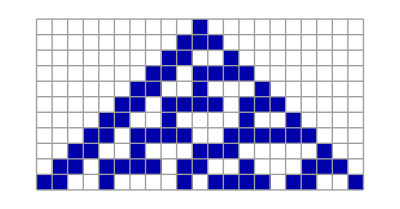

```mathematica
GraphicsRow[{ArrayPlot[CellularAutomaton[#, {{1}, 0}, 10], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]], Mesh->True], RulePlot[CellularAutomaton[#], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]]}]&[30]
```

So for instance, the initial condition here contains the sequence white, white, blue. The output of the rule for that sequence is blue, which is then placed in the next row. Moving one step to the right we have a sequence of white, blue, white. The output rule for that sequence is also blue, which is placed in the next row one cell to the right. This updating  procedure is repeated for all the subsequences at each row down the page.

This particular CA, rule 30, as its called, is important because its one of the simplest CAs that can generate complex behavior. So, starting from this simple initial condition of a single black cell, and following these eight rules, the program generates a pattern that is completely random:

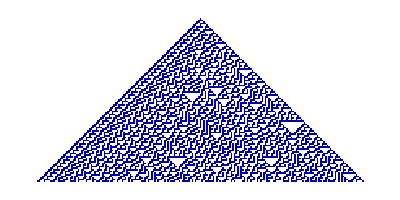

```mathematica
ArrayPlot[CellularAutomaton[30, {{1}, 0}, 100], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]]
```

Coincidentally, this rule is used as a cryptographic algorithm for generating key-pairs. And in fact, one of the directions of future work that were interested in is using it to engineer a cryptocurrency.

But I’m not going to discuss that here, instead, in light of trying to model the challenges of computer security, we’re going to look at how we can use CAs as a minimal model for a software system.

### A Minimal Model for a Software System

Rule 30, while complex, doesn’t seem to be doing any “useful computation” of the kind we’re used to seeing in software systems. But, Wolfram, in his book New Kind of Science, actually presented some CAs that can do useful computation. One example is the CA shown below, which can be thought of as a procedure for doubling its input:

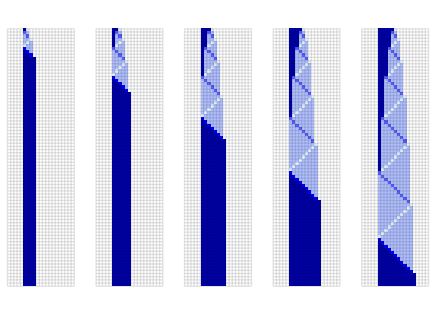

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, ImageSize->{Automatic, 300}]]@@@#]&@caperts[[1]]
]
```

The initial row, contains a string of two colored cells: one dark blue and one light blue. After running the rules for some number of steps, the final row contains a string of four colored cells, twice that of the initial row. The next panel has an initial condition with a string of three colored cells: two dark blue and one light blue. After running the same rules on this initial condition, the final row contains a string of six colored cells, twice the number from the initial row.

We can see from the pattern this calculation is performed in a very sequential manner, much like the way engineered software systems perform computation.

### Modeling an Attacker

Now that we have this minimal model for an engineered software program, we can model an attacker by perturbing cells in the pattern, and observe the resulting behavior.

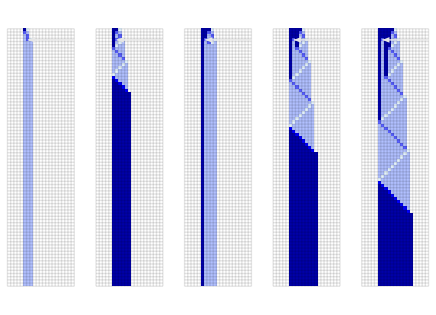

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Medium],GrayLevel[.9], Haloing[Red, 1.25]],"ArrowDirection"->Left,"InitialIndex"->0, ImageSize->{Automatic, 300}]]@@@#]&@caperts[[2]]
]
```

In some cases, like the second panel, the perturbation makes basically no change to the system, almost like changing an arbitrary print statement in the code of the program.

In the first and third panel, the perturbation, results in some trivial behavior, almost like killing the program immediately. In these cases, in contrast to the first panel, the resulting output is incorrect. In the fourth and fifth panel, the error is much more subtle, only slightly altering the behavior of the system, kind of like running a for-loop one too many times.

One thing to note, is with this CA at least, the resulting perturbations don’t lead to whole new classes of behavior, limiting the ability of an attacker to compromise the system. But what about other CAs?

### A More Efficient Procedure

We can look at at other CAs perform the doubling procedure “more efficiently”, i.e. in fewer steps:

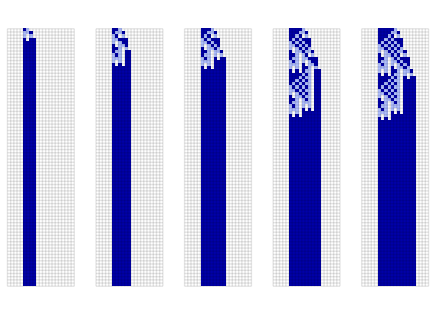

```mathematica
SeedRandom[111000+8];Module[{rule = {837428508144, 3, 1}, ca,capert,  pert = <|{30,9}->2|>, colrules = {0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, caperts},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, ImageSize->{Automatic, 300}]]@@@#]&@caperts[[1]]
]
```

This CA, instead of working in a sequential manner, essentially parallelizes the computation, resulting in the algorithm taking fewer steps. So what happens if we perturb this CA?

We can see that an intelligent attacker using the right perturbation has the ability to change the behavior faster than in the previous CA. With this particular perturbation, or compromise, the attacker can get the program to give an output that is too large for each input:

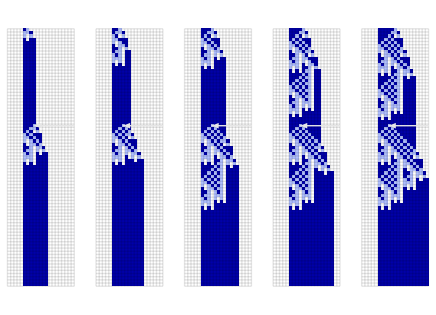

```mathematica
SeedRandom[111000+8];Module[{rule = {837428508144, 3, 1}, ca,capert,  pert = <|{30,9}->2|>, colrules = {0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, caperts},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Medium],GrayLevel[.9], Haloing[Red, 1]],"ArrowDirection"->Left,"InitialIndex"->0, ImageSize->{Automatic, 300}]]@@@#]&@caperts[[2]]
]
```

One way to think about this is, when using a more sophisticated procedure, the program becomes more malleable to attackers.

### A Larger Attack Surface

Along similar lines, we can look at what happens if the attacker is able to perturb not just cells in the pattern but an entire rule, effectively increases the surface of attack.

So here is the pattern and rules for our more efficient CA:

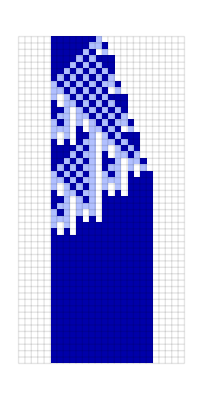

```mathematica
GraphicsRow[{RulePlot[CellularAutomaton[{837428508144, 3, 1}],ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}], ArrayPlot[CellularAutomaton[{837428508144, 3, 1},{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, Mesh->True, MeshStyle->Opacity[.1]]}, ImageSize->{Automatic, 300}]
```

Now, on the top we arrange the output of all our rules in a row, and change a single rule in that row from dark blue to light blue, shown by the red arrow:

```mathematica
RuleSequencePlot[{n_, k_, r_}, ops:OptionsPattern[{ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= 
ArrayPlot[{IntegerDigits[n, k, k^(2r+1)]},ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize], ops]
```

```mathematica
Module[{rule ={837428508144, 3, 1},sp,cf, is, murule = {837471554865,3,1}},
is = {200, Automatic};
 sp = RuleSequencePlot[rule,ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]},  ImageSize->is]; 
GraphicsRow[GraphicsColumn/@
{{sp, ArrayPlot[CellularAutomaton[rule,{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, ImageSize->is, Mesh->True, MeshStyle->Opacity[.1]]},
{Show[RuleSequencePlot[murule,ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]},  ImageSize->is],
With[{loc = SparseArray[{Subtract@@(IntegerDigits[#1, #2, #2^(2#3+1)]&@@@{murule, rule})}]["ExplicitPositions"][[1, 2]] -.5},
Graphics[{Style[Text["Compromise", {loc, 12}], Italic],Red, Arrowheads[.085],Thick,Arrow[{{loc , 10}, {loc, 1}}]}]]
, ImageSize->is],
ArrayPlot[CellularAutomaton[murule,{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, ImageSize->is, Mesh->True, MeshStyle->Opacity[.1]]}
}, Alignment->Bottom]]
```

-Graphics-

And as you may expect, the resulting change to the pattern is much more drastic.

And in fact, if we run this compromised rule for many more steps, we can see that its now capable of an almost infinite number of new behaviors:

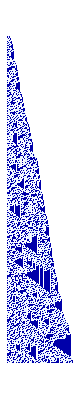

```mathematica
GraphicsRow[Table[
SeedRandom[111170+30];ArrayPlot[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[{837428508144, 3, 1}],{Join[Table[1,4],{2}],0},{{1000*i, 1000*(i+1)},Automatic}], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]],{i,0, 4}] , ImageSize->{300, Automatic}]
```

### Conclusion

One thing I’I think we’ve seen from this course is just how difficult computer security is. And I believe the reason can be seen from the experiments that I’ve highlighted here. Namely, as Stephen Wolfram discovered with rule-30 back in early 1980s, even the simplest programs are capable of arbitrarily complex behavior. And therefore as engineers trying to limit what an attacker can do to a software system, we are essentially fighting what Stephen calls computational irreducibility.

### Future work

A common reaction to these minimal models is to say that they are nothing like the practical systems used in the real world. But actually, as we’ve seen, even the simplest of  cellular automata are capable of arbitrary complexity. And in fact, it has been shown that cellular automata are what’s called Turing-complete. In other words, they can be made to emulate any program of arbitrary sophistication. As an example of this, Wolfram has constructed a CA that can compute the prime numbers:

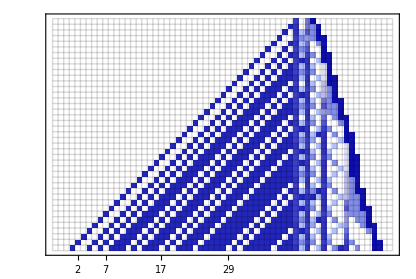

```mathematica
With[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={{10,0,4,8},0}},Show[ArrayPlot[CellularAutomaton[rule,init,{{0,40},{-43,17}}],Mesh->True,MeshStyle->Opacity[.15],ImageSize->500, ColorFunction->(Blend[{White,Darker[Blue], RGBColor[0.696, 0.752, 1]}, #]&), TicksStyle->GrayLevel[.25],Frame->True,FrameTicksStyle->GrayLevel[.25],FrameTicks->{False, Table[{Prime[i] + 3, Prime[i]}, {i, 1,12}], False, False}]]]
```

So one thing that we can look at in the future is what happens when we perturb these CAs running more complicated procedures?

Overall, in this article, I’ve hoped to have convinced the reader that using these simple computational models, we can study not just individual algorithms and methods of attack, but also look at computer security at a higher level and draw conclusions about the field as whole. I think this is a fascinating line of research and one that I plan on continuing after this course. Thank you for reading and thank you for a fun semester!